```mathematica
(*Pacote FeynmanRules*)
$FeynRulesPath=SetDirectory[FileNameJoin[{NotebookDirectory[],"feynrules-current"}]](*Define-se o diretório do pacote FeynRules, documentado em seu site oficialhttps://feynrules.irmp.ucl.ac.be/Nonehttps://feynrules.irmp.ucl.ac.be/HyperlinkActionRecycledHyperlinkActive*);
<<FeynRules`(*Checa-se o bom carregamento do pacote (alguns erros podem aparecer, são ignoráveis)*);
SetDirectory[$FeynRulesPath<>"/Models/SM"](*Defin-se o diretório do modelo do Modelo Padrão*);
LoadModel["SM.fr"](*Carrega-se o modelo do Modelo Padrão*);
LoadRestriction["Massless.rst","DiagonalCKM.rst"](*Carrega-se as restrições do Modelo Padrão*);
FeynmanGauge=True;
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,S] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,PS] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,L] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,S] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,PS] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,L] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,S] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,PS] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,L] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

This model implementation was created by

N. Christensen

C. Duhr

B. Fuks

Model Version: 1.4.7

http://feynrules.phys.ucl.ac.be/view/Main/StandardModel

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Standard Model loaded.

Global`a$::shdw: Symbol a$ appears in multiple contexts {Global`,FeynRules`}; definitions in context Global` may shadow or be shadowed by other definitions.

Loading restrictions from Massless.rst :  / 18

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
normLortz[x_,y_]:=(x[[1]]*y[[1]])-(x[[2]]*y[[2]])-(x[[3]]*y[[3]])-(x[[4]]*y[[4]]);
	(*com a assinatura da métrica Lorentziana dada por (+,-,-,-)*)
p1={p10,p11,p12,p13};
p2={p20,p21,p22,p23};
p3={p30,p31,p32,p33};
p4={p40,p41,p42,p43};
	(*definição dos 4-momentos inicialmente genéricos*)
```

```mathematica
sups1={e>0,g>0,λ>0,α==e^2/(4π),
normLortz[p1+p2,p1+p2]==s,
(*normLortz[p3+p4,p3+p4]==s,*)
normLortz[p1-p3,p1-p3]==t,
(*normLortz[p2-p4,p2-p4]==t,*)
normLortz[p1-p4,p1-p4]==u
(*normLortz[p2-p3,p2-p3]==u*)
};
	(*constante de acomplamento e variáveis de mandelstam; são as suposições que vão ser usadas nos cálculos*) 
sups2={
(p12 p22+p13 p23-p20 p30+p21 p31+p22 p32+p23 p33-p30 p40-p10 (p20+p40)+p31 p41+p11 (p21+p41)+p12 p42+p32 p42+p13 p43+p33 p43)==s-u,
(p12 p22+p13 p23-p10 (p20+p30)+p11 (p21+p31)+p12 p32+p13 p33-p20 p40-p30 p40+p21 p41+p31 p41+p22 p42+p32 p42+p23 p43+p33 p43)==s-t
};
sups3={

}
```

```mathematica
vert[g_]:=ⅈ*g;
	(*Cada vértice dá um fator (-ⅈg)*)
propEsc[p_,m_]:=ⅈ/(normLortz[p,p]-m^2);
propFot[p_]:=-ⅈ/normLortz[p,p];
	(*O propagador depende do diagrama que contribue*)
mDiagramaQEDescalar[m_,g_,numVert_,numPropFot_,pIn_,pOut_,pPropg_]:=
(vert[g]^numVert)*
(propFot[pPropg]^numPropFot)*
(normLortz[pIn,pOut])*(ⅈ);
	(*Os fatores ⅈϵ foram retirados pois  e estamos no gauge de Feynman*)
	(*constantes como c e ℏ já estão definidos como 1*)
ℳQEDEsc=mDiagramaQEDescalar(*Um alias para diminuir o tamanho da função*);
```

```mathematica
crossSectionQEDCM[m_,g_,s_,t_,u_]:=(1/(64*π^2*normLortz[p1+p2,p1+p2]))*Abs[(ℳQEDEsc[m,g,2,1,p1+p2,p3+p4,p1+p2]*s)+(ℳQEDEsc[m,g,2,1,p1+p3,p2+p4,p1-p3]*t)+(ℳQEDEsc[m,g,2,1,p1+p4,p2+p3,p1-p4]*u)]^2;
(*O total será a soma das contribuções, e neste caso apenas os diagramas T e U*)
dσdΩ[m_,g_,s_,t_,u_]:=Simplify[Simplify[crossSectionQEDCM[m,g,s,t,u],Assumptions->sups1],Assumptions->sups2];
	(*Um alias para diminuir o tamanho da função, assumir acoplamentos positivos e assumir as variáveis de Mandelstam e suas relações*);
```

```mathematica
dσdΩ[Subscript[m, e],e,0,1,1]
```

(α^2 Abs[(t^2+u^2-s (t+u))/(t u)]^2)/(4 s)

```mathematica
$FeynRulesPath=SetDirectory[FileNameJoin[{NotebookDirectory[],"feynrules-current"}]];
<<FeynRules`
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,S] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,PS] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,L] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,S] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,PS] is Protected.

SetDelayed::write: Tag MatrixSymbol in MatrixSymbol[id_,L] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

```mathematica
<<FeynArts`
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 1 Generic, 1 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 1 Generic, 1 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

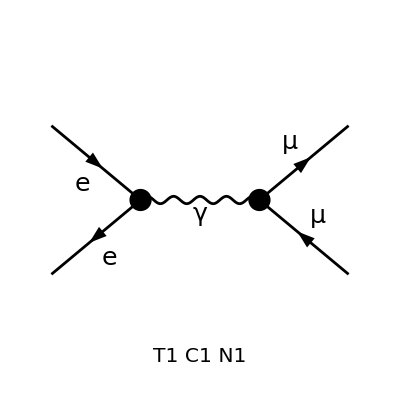

FeynArtsGraphics[{e,e}→{\mu,\mu}][([T1 C1 N1])]

```mathematica
Paint[InsertFields[CreateTopologies[0,2->2],{F[1,{1}],-F[1,{1}]}->{F[1,{2}],-F[1,{2}]},Model->"QED"],ColumnsXRows->1,PaintLevel->{Classes}]
```

```mathematica
CreateFeynAmp[InsertFields[CreateTopologies[0,2->2],{F[1,{1}],-F[1,{1}]}->{F[1,{2}],-F[1,{2}]},Model->"QED"]]
```

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 1 Generic, 1 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

FeynAmpList[Process→{{F[1,{1}],p1,ME,-Charge},{-F[1,{1}],p2,ME,Charge}}→{{F[1,{2}],k1,MM,-Charge},{-F[1,{2}],k2,MM,Charge}},Model→{QED},GenericModel→{Lorentz},AmplitudeLevel→{Generic,Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1],Integral[],RelativeCF v̄[p2,Mass[F[1,{1}]]].(ga[Lor1].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor1].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).u[p1,Mass[F[1,{1}]]] ū[k1,Mass[F[1,{2}]]].(ga[Lor2].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor2].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).v[k2,Mass[F[1,{2}]]] g[Lor1,Lor2] 1/((k1+k2)^2-Mass[V[Gen5],Internal]^2),{Mass[F[1,{1}]],Mass[F[1,{1}]],Mass[F[1,{2}]],Mass[F[1,{2}]],Mass[V[Gen5],Internal],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],RelativeCF}→Insertions[Classes][{ME,ME,MM,MM,0,ⅈ EL,ⅈ EL,ⅈ EL,ⅈ EL,1}]]]

```mathematica
decays=ComputeWidths[FeynmanRules[LSM]];
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 2 cores

Collecting the different structures that enter the vertex.

98 possible non-zero vertices have been found -> starting the computation:  / 98.

93 vertices obtained.

Flavor expansion of the vertices distributed over 2 cores:  / 93

Computing the squared matrix elements relevant for the 1->2 decays:

/ 40

Decay::Overwrite: Warning: Previous results will be overwritten.

```mathematica
BranchingRatio[{gamma,b,t}]
```

Decay::NumMass: Mass is not numerical. Cannot decide whether decay channel is open.

Decay::Channel: Decay channel not found.